```mathematica
base ={Circle[{0,0}], Circle[{0,0}, 0.8], Circle[{0,0}, 0.6]};
```

```mathematica
dividers = Table[Line[{0.6 {Sin[theta + Pi/26], Cos[theta + Pi/26]},  {Sin[theta + Pi/26], Cos[theta + Pi/26]}}], {theta, 0, 2 Pi, 2Pi / 26}];
```

```mathematica
alphabet = Table[ToUpperCase[FromLetterNumber[i]], {i, 1, 26}];
```

```mathematica
ringText[radius_, offset_, fontsize_, text_, color_] := Table[Text[Style[text[[1 + Mod[i  + offset, 26]]], FontWeight->"Bold", FontSize-> fontsize, FontColor->color], radius {Sin[i Pi/13], Cos[i Pi / 13]}, {0,0},{Cos[i Pi/13], -Sin[i Pi / 13]}], {i, 1, 26}]
```

```mathematica
ring[offset_] := Graphics[Join[base,dividers, ringText[0.7, offset, 16, alphabet,Black], ringText[0.9, 0, 18, alphabet,Red],
{Text[Style[alphabet[[offset + 1]], FontSize-> 40]]}]]
```

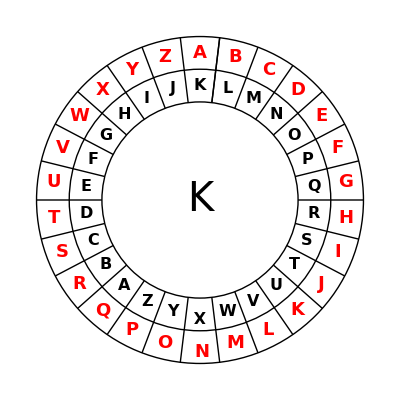

```mathematica
ring[10]
```

```mathematica
illustrate[offset_] := Graphics[
Join[
base,
dividers, 
ringText[0.75, offset, 12, alphabet, Black],
ringText[0.65, offset, 12, codedCounts, DarkGreen],
ringText[0.95, 0, 14, alphabet, Red],
ringText[0.85, 0, 14, stdCounts, Blue], 
{Text[Style[alphabet[[offset + 1]], FontSize-> 40]]}]]
```

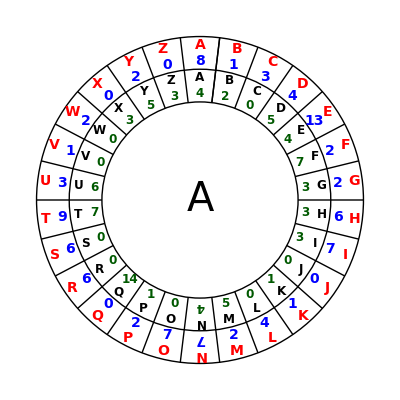

```mathematica
illustrate[0]
```

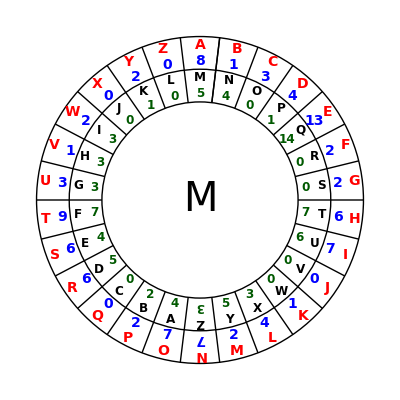

```mathematica
illustrate[12]
```

```mathematica
stdCounts = {8,1,3,4,13,2,2,6,7,0,1,4,2,7,7,2,0,6,6,9,3,1,2,0,2, 0}
```

{8,1,3,4,13,2,2,6,7,0,1,4,2,7,7,2,0,6,6,9,3,1,2,0,2,0}

```mathematica
{0, 8,1,3,4,13,2,2,6,7,0,1,4,2,7,7,2,0,6,6,9,3,1,2,0,2}
```

```mathematica
codedCounts = {4,2,0,5,4,7,3,3,3,0,1,0,5,4,0,1,14,0,0,7,6,0,0,3,5,3}
```

{4,2,0,5,4,7,3,3,3,0,1,0,5,4,0,1,14,0,0,7,6,0,0,3,5,3}